```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
dir = "Desktop/Q-Balls/fortran_files";
```

```mathematica
tab1= Import[FileNameJoin[{dir, "phi_0=1_06.dat"}],"Table"];
tab2= Import[FileNameJoin[{dir, "phi_0=1_05.dat"}],"Table"];
tab3= Import[FileNameJoin[{dir, "phi_0=1.dat"}],"Table"];
tab4= Import[FileNameJoin[{dir, "phi_0=0_743.dat"}],"Table"];
tab5= Import[FileNameJoin[{dir, "phi_0=0_5.dat"}],"Table"];
tab6= Import[FileNameJoin[{dir, "phi_0=0_4.dat"}],"Table"];
```

```mathematica
p1=ListPlot[Table[{tab1⟦i,1⟧,tab1⟦i,5⟧},{i,1,Length[tab1]}],PlotStyle->colors[[5]],Joined->True];
p2=ListPlot[Table[{tab2⟦i,1⟧,tab2⟦i,5⟧},{i,1,Length[tab2]}],PlotStyle->colors[[6]],Joined->True];
p3=ListPlot[Table[{tab3⟦i,1⟧,tab3⟦i,5⟧},{i,1,Length[tab3]}],PlotStyle->colors[[7]],Joined->True];
p4=ListPlot[Table[{tab4⟦i,1⟧,tab4⟦i,5⟧},{i,1,Length[tab4]}],PlotStyle->colors[[8]],Joined->True];
p5=ListPlot[Table[{tab5⟦i,1⟧,tab5⟦i,5⟧},{i,1,Length[tab5]}],PlotStyle->colors[[9]],Joined->True];
p6=ListPlot[Table[{tab6⟦i,1⟧,tab6⟦i,5⟧},{i,1,Length[tab6]}],PlotStyle->colors[[10]],Joined->True];

q1=ListPlot[Table[{tab1⟦i,1⟧,tab1⟦i,6⟧},{i,1,Length[tab1]}],PlotStyle->colors[[5]],Joined->True];
q2=ListPlot[Table[{tab2⟦i,1⟧,tab2⟦i,6⟧},{i,1,Length[tab2]}],PlotStyle->colors[[6]],Joined->True];
q3=ListPlot[Table[{tab3⟦i,1⟧,tab3⟦i,6⟧},{i,1,Length[tab3]}],PlotStyle->colors[[7]],Joined->True];
q4=ListPlot[Table[{tab4⟦i,1⟧,tab4⟦i,6⟧},{i,1,Length[tab4]}],PlotStyle->colors[[8]],Joined->True];
q5=ListPlot[Table[{tab5⟦i,1⟧,tab5⟦i,6⟧},{i,1,Length[tab5]}],PlotStyle->colors[[9]],Joined->True];
q6=ListPlot[Table[{tab6⟦i,1⟧,tab6⟦i,6⟧},{i,1,Length[tab6]}],PlotStyle->colors[[10]],Joined->True];

g1=ListPlot[Table[{tab1⟦i,1⟧,tab1⟦i,3⟧},{i,1,Length[tab1]}],PlotStyle->colors[[5]],Joined->True];
g2=ListPlot[Table[{tab2⟦i,1⟧,tab2⟦i,3⟧},{i,1,Length[tab2]}],PlotStyle->colors[[6]],Joined->True];
g3=ListPlot[Table[{tab3⟦i,1⟧,tab3⟦i,3⟧},{i,1,Length[tab3]}],PlotStyle->colors[[7]],Joined->True];
g4=ListPlot[Table[{tab4⟦i,1⟧,tab4⟦i,3⟧},{i,1,Length[tab4]}],PlotStyle->colors[[8]],Joined->True];
g5=ListPlot[Table[{tab5⟦i,1⟧,tab5⟦i,3⟧},{i,1,Length[tab5]}],PlotStyle->colors[[9]],Joined->True];
g6=ListPlot[Table[{tab6⟦i,1⟧,tab6⟦i,3⟧},{i,1,Length[tab6]}],PlotStyle->colors[[10]],Joined->True];
```

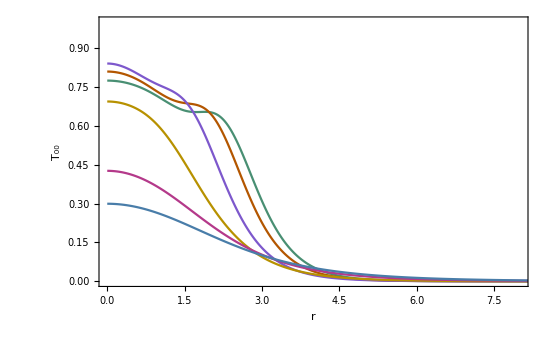

```mathematica
Show[{q1,q2,q3,q4,q5,q6},PlotRange->{{0,8},{0,1}},Epilog->Inset[Framed[Column[{LineLegend[{colors[[5]]},{"ψ_0 = 1.06"}],LineLegend[{colors[[6]]},{"ψ_0 = 1.05"}],LineLegend[{colors[[7]]},{"ψ_0 = 1.0"}],LineLegend[{colors[[8]]},{"ψ_0 = 0.743"}],LineLegend[{colors[[9]]},{"ψ_0 = 0.5"}],LineLegend[{colors[[10]]},{"ψ_0 = 0.4"}]}],RoundingRadius->5],Scaled[{0.8,0.65}]],PlotRange->{{0,15},{0,4}},FrameLabel-> {"r","T_00"},Axes-> False,LabelStyle-> {Bold,FontSize-> 12},ImageSize-> 550,Frame-> True]
```

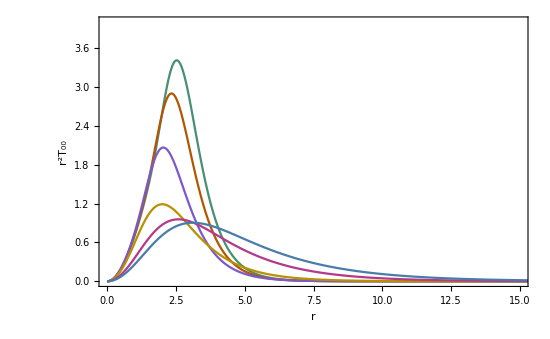

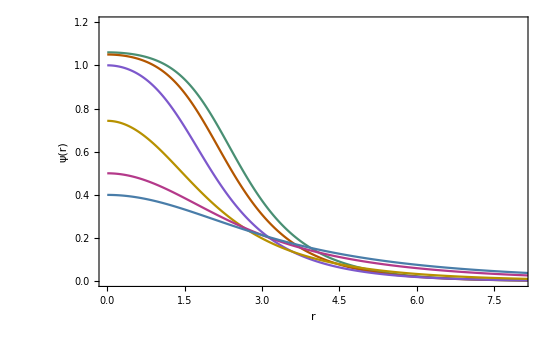

```mathematica
t00=Show[{p1,p2,p3,p4,p5,p6},Frame-> True,Epilog->Inset[Framed[Column[{LineLegend[{colors[[5]]},{"ψ_0 = 1.06"}],LineLegend[{colors[[6]]},{"ψ_0 = 1.05"}],LineLegend[{colors[[7]]},{"ψ_0 = 1.0"}],LineLegend[{colors[[8]]},{"ψ_0 = 0.743"}],LineLegend[{colors[[9]]},{"ψ_0 = 0.5"}],LineLegend[{colors[[10]]},{"ψ_0 = 0.4"}]}],RoundingRadius->5],Scaled[{0.8,0.65}]],PlotRange->{{0,15},{0,4}},FrameLabel-> {"r","r^2T_00"},Axes-> False,LabelStyle-> {Bold,FontSize-> 12},ImageSize-> 550]
phixr=Show[{g1,g2,g3,g4,g5,g6},Frame-> True,Epilog->Inset[Framed[Column[{LineLegend[{colors[[5]]},{"ψ_0 = 1.06"}],LineLegend[{colors[[6]]},{"ψ_0 = 1.05"}],LineLegend[{colors[[7]]},{"ψ_0 = 1.0"}],LineLegend[{colors[[8]]},{"ψ_0 = 0.743"}],LineLegend[{colors[[9]]},{"ψ_0 = 0.5"}],LineLegend[{colors[[10]]},{"ψ_0 = 0.4"}]}],RoundingRadius->5],Scaled[{0.8,0.65}]],PlotRange->{{0,8},{0,1.2}},FrameLabel-> {"r","ψ(r)"},Axes-> False,LabelStyle-> {Bold,FontSize-> 12},ImageSize-> 550]
```

```mathematica
data1= Import[FileNameJoin[{dir, "data.dat"}],"Table"];
datasort=SortBy[data1,First];
```

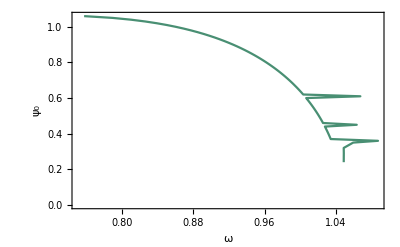

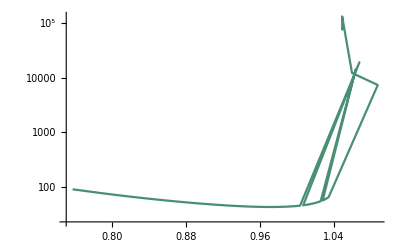

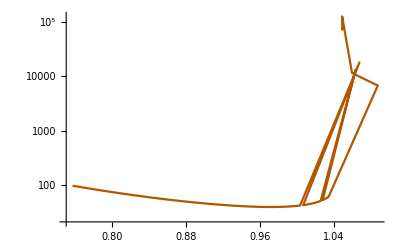

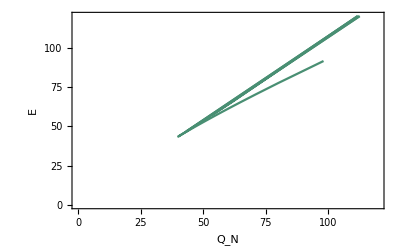

```mathematica
Subscript[ωxϕ, 0]=ListPlot[Table[{datasort⟦i,2⟧,datasort⟦i,1⟧},{i,1,Length[datasort]}],Joined->True,PlotStyle->colors[[5]],Frame->True,FrameLabel->{ω,Subscript[ψ, 0]},PlotRange->All,LabelStyle-> {Bold,FontSize-> 12}]
ωpxE=ListLogPlot[Table[{datasort⟦i,2⟧,datasort⟦i,4⟧},{i,1,Length[datasort]}],Joined->True,PlotStyle->colors[[5]],PlotRange->All]
ωpxQ=ListLogPlot[Table[{datasort⟦i,2⟧,datasort⟦i,3⟧},{i,1,Length[datasort]}],Joined->True,PlotStyle->colors[[6]],PlotRange->All]
QxE=ListPlot[Table[{datasort⟦i,3⟧,datasort⟦i,4⟧},{i,1,Length[datasort]}],Joined->True,PlotStyle->colors[[5]],Frame->True,FrameLabel->{Subscript[Q, N],"E"},PlotRange->{{0,120},{0,120}},Axes->True,LabelStyle-> {Bold,FontSize-> 12}]
```

```mathematica
Export["ωxϕ_0.pdf",Subscript[ωxϕ, 0]]
```

ωxϕ_0.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["\!\(\*SubscriptBox[\(ωxϕ\), \(0\)]\).pdf"]]]
```

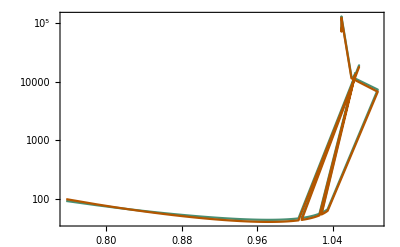

```mathematica
p12=Show[{ωpxE,ωpxQ},Epilog->Inset[Framed[Column[{LineLegend[{colors[[5]]},{"E"}],LineLegend[{colors[[6]]},{"Q_N"}]}],RoundingRadius->5],Scaled[{0.8,0.75}]],PlotRange->All,FrameLabel-> {ω},Frame->True,Axes-> False,LabelStyle-> {Bold,FontSize-> 12},Joined-> True]
```

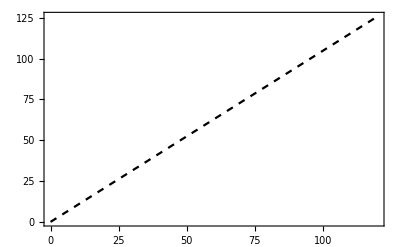

```mathematica
freeboson=Plot[√1.1 x,{x,0,120},PlotStyle->{Black,Dashed},Frame->True]
```

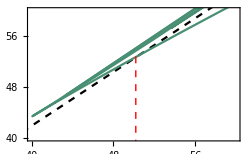

```mathematica
pt5=Graphics[{PointSize[0.0],Point[{50.2,52.8}]}];
line5=Line[{{50.2,52.8},{50.2,0}}];
line6=Graphics[{Dashed,Red,line5}];
txt5=Graphics[Text["ω_s",{50.2,5},{2,-1}]];
pzoom=Show[freeboson,QxE,line6,PlotRange->{{40,60},{40,60}},Axes->True,Frame->True,ImageSize->250]
```

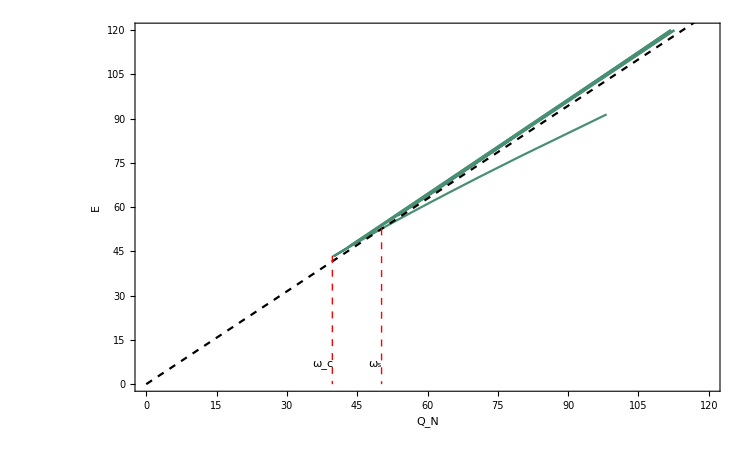

```mathematica
pt2=Graphics[{PointSize[0.0],Point[{39.7,43.5}]}];
line2=Line[{{39.7,43.5},{39.7,0}}];
line3=Graphics[{Dashed,Red,line2}];
txt2=Graphics[Text["ω_c",{40,5},{2,-1}]];

pt5=Graphics[{PointSize[0.0],Point[{50.2,52.8}]}];
line5=Line[{{50.2,52.8},{50.2,0}}];
line6=Graphics[{Dashed,Red,line5}];
txt5=Graphics[Text["ω_s",{50.2,5},{2,-1}]];


p33=Show[{QxE,freeboson,pt2,line3,txt2,pt5,line6,txt5},Epilog-> {Inset[pzoom,{30,85}],Inset[Framed[Column[{LineLegend[{colors[[5]]},{"Q-balls"}],LineLegend[{Dashed,Blue},{"Free bosons"}]}],RoundingRadius->5],Scaled[{0.8,0.2}]]},ImageSize->750]
```

```mathematica
Export["p33.pdf",p33]
```

p33.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["p33.pdf"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["p33.pdf"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["p33.pdf"]]]
```

```mathematica
FindMinimum[1/2(1.1 x^2-2 x^4+x^6),x]
```

{0.0486792,{x→0.972396}}

```mathematica
FindMaximum[1/2 ω1^2 x^2-1/2(1.1 x^2-2 x^4+x^6),{x,1}]
```

{0.404724,{x→1.12089}}

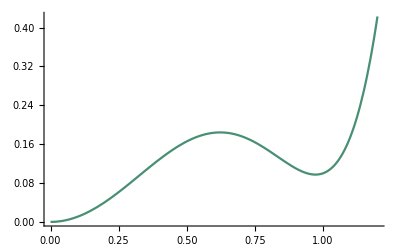

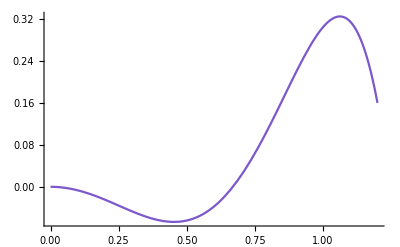

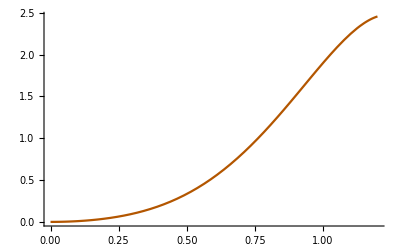

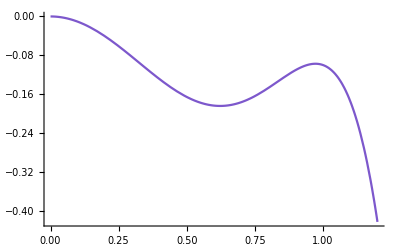

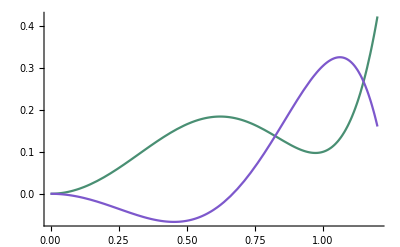

```mathematica
pot1=Plot[{1.1 x^2-2 x^4+x^6},{x,0,1.2},PlotRange->All,PlotStyle->colors[[5]]]
ω1=0.9;
ω2 = 2;
ω3 = 0.01;
potef1=Plot[{1/2 ω1^2 x^2-(1.1 x^2-2 x^4+x^6)},{x,0,1.2},PlotRange->All,PlotStyle->colors[[7]]]
potef2=Plot[{1/2 ω2^2 x^2-(1.1 x^2-2 x^4+x^6)},{x,0,1.2},PlotRange->All,PlotStyle->colors[[6]]]
potef3=Plot[{1/2 ω3^2 x^2-(1.1 x^2-2 x^4+x^6)},{x,0,1.2},PlotRange->All,PlotStyle->colors[[7]]]
Show[{pot1,potef1}]
```

```mathematica
min1=FindMinimum[1.1 x^0-2 x^2+x^4,{x,1.2}]
```

{0.1,{x→1.}}

```mathematica
pt1=Graphics[{PointSize[0.02],Point[{1,0.1}]}];
line=Line[{{1.0,0},{1.0,0.1}}];
line2=Graphics[{Dashed,line}];
txt=Graphics[Text["U(ψ_)",{1,0.13},{0,-1}]];
```

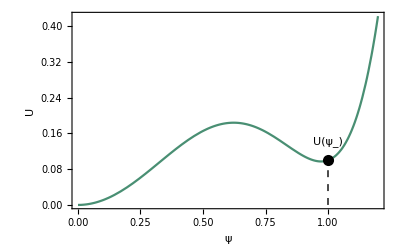

```mathematica
pot=Show[{pot1,pt1,line2,txt},Frame-> True,Epilog->Inset[Framed[Column[{LineLegend[{colors[[5]]},{"1.1 ψ^2- 2 ψ^4+ψ^6"}]}],RoundingRadius->5],Scaled[{0.3,0.75}]],FrameLabel-> {ψ,U},Frame->True,Axes-> True,LabelStyle-> {Bold,FontSize-> 12}]
```

```mathematica
Export["pot.pdf",pot]
```

pot.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["pot.pdf"]]]
```

```mathematica
"pot.pdf"dddd
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["pot.pdf"]]]
```

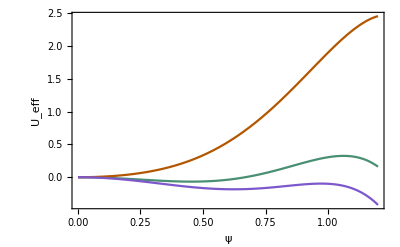

```mathematica
poteff=Show[{potef1,potef2,potef3},Epilog->Inset[Framed[Column[{LineLegend[{colors[[5]]},{"ω_- < ω < ω_+ "}],LineLegend[{colors[[6]]},{"ω > ω_+"}],LineLegend[{colors[[7]]},{"ω < ω_-"}]}],RoundingRadius->5],Scaled[{0.2,0.75}]],PlotRange->All,FrameLabel-> {"ψ","U_eff"},Frame->True,Axes-> True,LabelStyle-> {Bold,FontSize-> 12},Joined-> True]
```

```mathematica
Export["poteff.pdf",poteff]
```

poteff.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["poteff.pdf"]]]
```

```mathematica
√1.1
```

1.04881

```mathematica
√0.1
```

0.316228